Corso di Laboratorio Computazionale — Corso di Laurea in Matematica — Università di Padova.

Anno Accademico 2019-2020

# Esercizi 1. Grafica e teoria dei numeri

Notebook del gruppo Cammelli Tonanti.
Componenti del gruppo: Francesco Tognetti, Riccardo Cazzin.
Se ci sono stati collaborazioni o aiuti al di fuori del gruppo, dichiararli.
In collaborazione con
Aiutati da

## Esercizio 1.3 (Teorema dei numeri primi).

### Testo dell’esercizio

Il teorema dei numeri primi afferma che le funzioni π(n), n/(log(n)), li(n) sono asintotiche per n→∞. Investigare numericamente quest’affermazione.

### Svolgimento

Ricorrendo al risolutore di limiti interno a Mathematica, possiamo intravedere l’asintoticità per n→∞.

```mathematica
{
Limit[PrimePi[n]/(n/Log[n]),n->∞],
Limit[PrimePi[n]/LogIntegral[n],n->∞]
}
```

Occorre precisare che ciò non significa che il modulo della differenza tra due delle funzioni in esame sia infinitesimo. Come si vede nel grafico seguente, la differenza in valore assoluto tra π(n) e n/(log(n)) è tendenzialmente crescente. Dal grafico, però, non è chiaro quale α>0 sia tale che n^α sia asintotico a |π(n)-n/(log(n))| — né, in realtà, sono presenti elementi che assicurino l’esistenza di un tale α.

```mathematica
Manipulate[
LogLogPlot[
{
Abs[PrimePi[x]-x/Log[x]],
x^α
},
{x,10^k,10^(k+3)},
PlotStyle->{Red,Black},
PlotLegends->{TraditionalForm[Abs[PrimePi[x]-x/Log[x]]],TraditionalForm[x^α]},Ticks->{N@(10^Range[k,k+3]),Automatic}(*La N impedisce che i numeri sotto i tick compaiano per esteso anche quando troppo lunghi.*)
],
{k,Range[9]},(*Questa sintassi permette di ottenere un controllo a tendina anziché a slider.*)
{α,0.1,1}
]
```

Confrontando π(n) con li(n), seppur con oscillazioni più pronunciate, si ottiene ugualmente che la differenza in valore assoluto tra le due funzioni non è infinitesima, ma tendente a ∞ per n→∞. Anche in questo caso non è facile individuare “ad occhio” l’esponente β>0, se esiste, tale che n^β sia asintotico a |π(n)-li(n)|.

```mathematica
Manipulate[
LogLogPlot[
{
Abs[PrimePi[x]-LogIntegral[x]],
x^β
},
{x,10^k,10^(k+2)},
PlotStyle->{Red,Black},
PlotLegends->{TraditionalForm[Abs[PrimePi[x]-LogIntegral[x]]],TraditionalForm[x^β]},Ticks->{N@(10^Range[k,k+2]),Automatic}
],
{k,Range[10]},
{β,0.3,.45}
]
```

Il grafico seguente indaga “visivamente” l’asintoticità di π(n) e n/(log(n)), ovvero mostra se il rapporto tra le due funzioni tende a 1. Si può notare che il rapporto è definitivamente decrescente ed inferiormente limitato da 1, ma il decadimento è molto lento.

```mathematica
Manipulate[
LogLogPlot[
PrimePi[x]/(x/Log[x]),
{x,10^k,10^(k+5)},
PlotStyle->Blue,Ticks->{N@(10^Range[k,k+5]),Automatic},PlotLegends->{TraditionalForm[Defer@(PrimePi[x]/(x/Log[x]))]},PlotRange->{.99,1.3}
],
{k,Range[0,9]}
]
```

L’asintoticità di π(n) e li(n), invece, è molto più evidente a partire dal grafico: già per n>10^5 il rapporto tra le due funzioni è “molto vicino” a 1.

```mathematica
Manipulate[
LogLogPlot[
LogIntegral[x]/PrimePi[x],
{x,10^k,10^(k+5)},
PlotStyle->Blue,Ticks->{N@(10^Range[k,k+5]),Automatic},PlotLegends->{TraditionalForm[PrimePi[x]/LogIntegral[x]]},PlotRange->{0.999,1.5}
],
{k,Range[9]}
]
```

(π(n) - n/ln(n))/(π(n))

```mathematica
Table[Abs[((PrimePi[n]-n/Log[n])/PrimePi[n]-(PrimePi[n]/(n/Log[n])-1))/(PrimePi[n]/(n/Log[n])-1)],{n,10^Range[16]}]//N
```

```mathematica
Manipulate[
LogLogPlot[{(PrimePi[x]-x/Log[x])/PrimePi[x],PrimePi[x]/(x/Log[x])-1},
{x,10^k,10^(k+3)},
(*PlotStyle->Blue,*)
Ticks->{N@(10^Range[k,k+3]),Automatic},PlotRange->{0.01,0.3}
],
{k,Range[9]}
]
```

```mathematica
Manipulate[
LogLogPlot[LogIntegral[x]/PrimePi[x]-1,
{x,10^k,10^(k+3)},
PlotStyle->Blue,
Ticks->{N@(10^Range[k,k+3]),Automatic}
],
{k,Range[9]}
]
```

## Esercizio 1.4 (Catenaria).

### Testo dell’esercizio

Se, nel piano xy, un cerchio di raggio r rotola senza strisciare sull’asse x, un punto P del cerchio descrive, nel piano xy, una curva chiamata catenaria, di equazioni parametriche

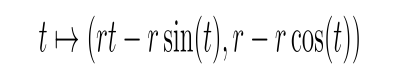

Produrre un’animazione (e magari un filmato) che mostra il cerchio (o un disco) che rotola, il punto P su di essa, e la curva descritta da P nel piano.

### Svolgimento

Ogni fotogramma dell’animazione deve contenere due strutture:

la ruota che gira;

la “scia” lasciata da P nel piano.

La ruota è composta da una circonferenza di raggio r che trasla, dal punto P sulla circonferenza che ruota e si sposta rimanendo sulla circonferenza e da due linee – un numero minimo di “raggi” della ruota – che seguono il movimento di P. La scia è una curva parametrizzata, mostrata di modo che sembri la “scia” lasciata da P.
Creiamo dapprima una funzione che computi il grafico ad un istante t dato. Tale funzione permette di scegliere il raggio r della circonferenza, l’angolo in senso orario θ di discostamento di P dal punto “più in basso” della circonferenza, il numero di archi che vogliamo vedere descritti dalla curva intorno allo 0 (funziona meglio con numeri pari) e l’istante t che vogliamo mostrare.

```mathematica
ClearAll["Global`*"]
```

```mathematica
rotolaFrame[r_,θ_,giri_,t_]:=Show[
Graphics[
{
{
Thick,Hue[0.1,0.1,0.1],
Circle[{t ,r},r]
},
{
Hue[0,0,0.6],
Line[{{t,r}+RotationMatrix[(-(θ+t))/r].{0,-r},{t,r}+RotationMatrix[(-(θ+t))/r+π].{0,-r}}],
Line[{{t,r}+RotationMatrix[(-(θ+t))/r+π/2].{0,-r},{t,r}+RotationMatrix[(-(θ+t))/r-π/2].{0,-r}}]
},
{
Red,PointSize[.007],
Point[{t,r}+RotationMatrix[(-(θ+t))/r].{0,-r}]
}
},
Axes->{True,False},Ticks->{Range[-giri π r,giri π r,IntegerPart[giri/2] π],None},PlotRange->{{-(giri π+1)r,(giri π+1) r},{-.1,2r+0.5}},ImageSize->Full
],
ParametricPlot[
r{u-Sin[u],1-Cos[u]}-{θ,0},
{u,-(giri π+1.01)r,(t+θ)/r},
PlotStyle->{Hue[1,0.5,1]}
]
]
```

```mathematica
rotolaFrame[3,π/3,4,7]
```

In seguito, creiamo un oggetto interattivo per dare un’idea dell’evoluzione della curva.

```mathematica
rotola[r_,θ_,giri_]:=Manipulate[
rotolaFrame[r,θ,giri,t],
{t,-(giri π+1)r,(giri π+1) r}
]
```

```mathematica
rotola[3,π/2,2]
```

Possiamo collezionare un numero sufficiente di immagini per creare una GIF fluida: utilizzando uno standard video consolidato, scegliamo di mostrare 30 fotogrammi al secondo.

```mathematica
rotolaExport[r_,θ_,giri_,secondi_]:=Export[NotebookDirectory[]<>"rotolando.gif",rotolaFrame[r,θ,giri,#]&/@Subdivide[-(giri π+1)r,(giri π+1) r,30secondi],ImageSize->1000,"DisplayDurations"->(1/30&/@Range[30secondi+1])]
```

```mathematica
rotolaExport[2,π/6,4,5]
```